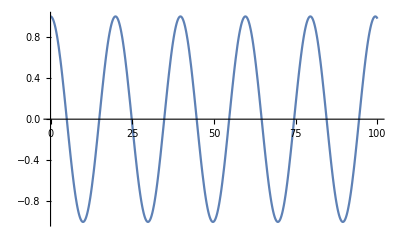

```mathematica
NDSolveValue[##]&@@({{x''[t]+μk W/L x[t]==0,x[0]==x0,x'[0]==xp0},x,{t,0,tf}}/.{μk->0.1,W->L,x0->1,xp0->0,tf->100});
Plot[%[t],{t,0,100}]
```

```mathematica
Manipulate[  With[{sol=NDSolve[{x''[t] +μk W/L x[t] == 0, x[0] == x0,x'[0] == xp0}, x,{t,0,tf}][[1]]},  Column[{Graphics[{  Blue,Disk[{-L,0},.25],Disk[{L,0},.25], Thickness[.0025],LightBlue,Table[Line[{{-L,0},{.25Cos[θ-tf]-L,.25Sin[θ-tf]}}],{θ,0,2π,π/3}], Table[Line[{{L,0},{.25Cos[θ+tf]+L,.25Sin[θ+tf]}}],{θ,0,2π,π/3}], Thickness[.005],Brown,Line[{{-L-.5+x[tf] /. sol,.25},{L+.5+x[tf] /. sol,.25}}],Darker@Green,Arrow[{{-L,.25},{-L+.1μk(L-x[tf] /. sol)W/(2L),.25}}],Arrow[{{L,.25},{L-.1μk(L+x[tf] /. sol)W/(2L),.25}}], Orange,Arrow[{{-L,.25},{-L,.25+.1(L-x[tf] /. sol)W/(2L)}}],Arrow[{{L,.25},{L,.25+.1(L+x[tf] /. sol)W/(2L)}}]},PlotRange->{{-2.1,2.1},{-.5,1.5}},ImageSize->400,Axes->{False,True},Ticks->False,AxesStyle->Dashed],  Plot[Evaluate[x[t] /. sol],{t,0,tf},PlotRange->{{0,10},{-.5,.5}},ImageSize->400,AxesLabel->{t,x[t]}]}]],  {{tf,10,Style["t",Italic]},0.1,10,.01,ImageSize->Tiny,Appearance->"Labeled"},{{μk,.5,Subscript["μ",Style["k",Italic]]},0.3,1.,.01,ImageSize->Tiny,Appearance->"Labeled"}, {{W,10.,Style["W",Italic]},10,20.,.01,ImageSize->Tiny,Appearance->"Labeled"},{{L,1.,Style["L",Italic]},1.,1.5,.01,ImageSize->Tiny,Appearance->"Labeled"},{{x0,-.25,"x(0)"},-.4,.4,.01,ImageSize->Tiny,Appearance->"Labeled"}, {{xp0,.25,"x'(0)"},-.4,.4,.01,ImageSize->Tiny,Appearance->"Labeled"},ControlPlacement->Left]
```

```mathematica
Clear["Global`*"]
μk=1;
W=4;
L=0.5;
x0=0;
xp0=1;
lst=Table[With[{sol=NDSolve[{x''[t] +μk W/L x[t] == 0, x[0] == x0,x'[0] == xp0}, x,{t,0,tf}][[1]]},
Graphics[{  Blue,Disk[{-L,0},.25],Disk[{L,0},.25], Thickness[.0025],LightBlue,Table[Line[{{-L,0},{.25Cos[θ-tf]-L,.25Sin[θ-tf]}}],{θ,0,2π,π/3}], Table[Line[{{L,0},{.25Cos[θ+tf]+L,.25Sin[θ+tf]}}],{θ,0,2π,π/3}], Thickness[.005],Brown,Line[{{-L-.5+x[tf] /. sol,.25},{L+.5+x[tf] /. sol,.25}}],Darker@Green,Arrow[{{-L,.25},{-L+.1μk(L-x[tf] /. sol)W/(2L),.25}}],Arrow[{{L,.25},{L-.1μk(L+x[tf] /. sol)W/(2L),.25}}], Orange,Arrow[{{-L,.25},{-L,.25+.1(L-x[tf] /. sol)W/(2L)}}],Arrow[{{L,.25},{L,.25+.1(L+x[tf] /. sol)W/(2L)}}]},PlotRange->{{-2.1,2.1},{-.5,1.5}},ImageSize->400,Axes->{False,True},Ticks->False,AxesStyle->Dashed]
]
,{tf,0,√(μk W/L)/2π,0.05}];
ListAnimate@lst
```

```mathematica
Export[NotebookDirectory[]<>"FrictionOscillator.gif",lst]
```

X:\Document\Project\CUPT 4th\Research\13 Friction Oscillator\FrictionOscillator.gif